# Thesis graphing analysis .nb

## Markku Alho

Licensing information, TBD. All rights reserved thus far.

## Section Initialization of functions and definitions

Initialization cells (blue background) should be evaluated when prompted. This section requires no user interaction.

```mathematica
(*Enable relative paths*)
SetDirectory[NotebookDirectory[]]
```

D:\graduverkko\filpromo17-teesiverkko\Graphing

### Language, char & string definitions

```mathematica
English=Entity["Language","English"];
specialcharsReplRules={"\\n"->" ","\r"->"\n"};
Dropstrs="(http://www.helsinki.fi/helka/index.htm)";
HTMLReplaceRule=x:("\\x"~~Repeated[HexadecimalCharacter,2]):>FromCharacterCode[Interpreter["HexInteger"][StringDrop[x,2]] ];
UnicodeReplaceRule=x:("\\u"~~Repeated[HexadecimalCharacter,4]):>FromCharacterCode[Interpreter["HexInteger"][StringDrop[x,2]] ];
charsetReplaceRules={HTMLReplaceRule,UnicodeReplaceRule};

(*Note: U+1F670 (et) not included, does not fit to Mathematica 16-bit encodings*)
(*ß is also expanded, in case there are (probably) different spelling conventions in the corpus. Might give some weird sss's in the output at the end. Maybe should be sz? Dunno.*)
(*Taken from Wikipedia ("Ligatures in Unicode"), includes Serbian/Croatian digraphs*)
unicodeLigatureReplRules={"\\ua732"->"AA","\\ua733"->"aa","\\u00c6"->"AE","\\u00e6"->"ae","\\ua734"->"AO","\\ua735"->"ao","\\ua736"->"AU","\\ua737"->"au",{"\\ua738","\\ua73a"}->"AV",{"\\ua739","\\ua73b"}->"av","\\ua73c"->"AY","\\ua73d"->"ay","\\ufb00"->"ff","\\ufb03"->"ffi","\\ufb04"->"ffl","\\ufb01"->"fi","\\ufb02"->"fl","\\u0152"->"OE","\\u0153"->"oe","\\ua74e"->"OO","\\ua74f"->"oo","\\u00df"->"ss","\\ufb06"->"st","\\ufb05"->"ft","\\ua728"->"TZ","\\ua729"->"tz","\\u1d6b"->"ue","\\ua760"->"VY","\\ua761"->"vy","\\u01f1"->"DZ","\\u01f2"->"Dz","\\u01f3"->"dz","\\u01c4"->"DŽ","\\u01c5"->"Dž","\\u01c6"->"dž","\\u0132"->"IJ","\\u0133"->"ij","\\u01c7"->"LJ","\\u01c8"->"Lj","\\u01c9"->"lj","\\u01ca"->"NJ","\\u01cb"->"Nj","\\u01cc"->"nj"};
(*Also expand possible actual unicode ligatures*)
unicodeLigatureReplRules2=KeyMap[StringReplace[#,UnicodeReplaceRule]&,Association@@unicodeLigatureReplRules]//Normal;

(* omfg. maybe these should also include HTML versions*)
```

### Function definitions

```mathematica
(* a re-scaler to approximate range ]0,1[ instead of [0,1]*)
ewRescale[ews_]:=Rescale[ews,MinMax[ews],{0+eps,1-eps}/.eps->0.01];
(*Split HELDA string outputs, note different delimiters and Unicode signifiers*)
split[xi_]:=Module[{delimiter,nextpos,out={},x=xi,i=1},{
(*Assume max 50 entries - there might be several languages of several fields (that should be in e.g. abstract) included in an entry )*)
While[i<50,
{
(*Get rid of Unicode specifier, if any*)
x=If[StringStartsQ[x,"u"],StringDrop[x,1],x];
(*Find the delimiter (assume a single character delimiter)*) 
delimiter=StringTake[x,1];
(*Replace with a temporary delimiter (is this necessary anymore?)*)
x=StringReplace[x,"\\"<>delimiter->"***TEMP***"];
(*Get the locations of the first pair of these delimiters*)
nextpos=StringPosition[x,delimiter,2][[1;;2,1]];
(*Take the string between delimiters and trim it - does the trimming/back subst do anything?*)
AppendTo[out,StringTake[x,nextpos]//StringTrim[#,delimiter]&//StringReplace[#,"***TEMP***"->delimiter]&];
(*Drop the extracted part from scanned string*)
x=StringDrop[x,nextpos];
(*Parsed*)
If[StringLength[x]<2,Break[]];
(*Get rid of comma and whitespace*)
x=StringDrop[x,2];

i++;
}];
out
}//Flatten]
(*Select the parts corresponding to a language from an array of metadata entries containing several languages, or the first entry if no match to language *)
prunelangs[x_,lang_]:=
Module[{entry,foo,i,j,out={},aps},{
For[i=1,i≤Length[x],i++,
{
entry=x[[i]];
If[StringLength[entry]==0,{AppendTo[out,{entry}],Echo["Empty entry at location "<>ToString[i]],Continue[]}];
foo=entry//split;
For[j=1,j≤Length[foo],j++,
{
foo[[j]]=If[StringStartsQ[foo[[j]],"Tiedekunta/Osasto – Fakultet/Sektion – Faculty"],StringDrop[foo[[j]],StringPosition[foo[[j]],"Tiivistelmä – Referat – Abstract",1][[1,2]]],foo[[j]]];
foo[[j]]=If[StringContainsQ[foo[[j]],"Säilytyspaikka – Förvaringställe – Where deposited"],StringTake[foo[[j]],StringPosition[foo[[j]],"Säilytyspaikka – Förvaringställe – Where deposited",1][[1,1]]-1],foo[[j]]];
foo[[j]]=StringDelete[foo[[j]],"Avainsanat – Nyckelord – Keywords"];
}];
foo=DeleteCases[foo,_?(StringContainsQ[#,Dropstrs]&)];
aps=If[Length[foo]>1,Select[foo,LanguageIdentify[#]==lang&,1],foo];

aps=If[Length[aps]==0,aps={""},aps];

AppendTo[out,aps[[1]] ] ;

}]
};

out]

(*A map-able version of the above. Select the parts corresponding to a language from an array of metadata entries containing several languages, or the first entry if no match to language *)
prunelang[x_,lang_]:=
Module[{entry=x,foo,i,j,out={},aps},
If[StringLength[entry]==0,Return[""]];
foo=entry//split;
For[j=1,j≤Length[foo],j++,
{
foo[[j]]=If[StringStartsQ[ foo[[j]], "Tiedekunta/Osasto – Fakultet/Sektion – Faculty"], StringDrop[foo[[j]], StringPosition[foo[[j]],"Tiivistelmä – Referat – Abstract",1][[1,2]]],foo[[j]]];
foo[[j]]=If[StringContainsQ[foo[[j]],"Säilytyspaikka – Förvaringställe – Where deposited"],StringTake[foo[[j]],StringPosition[foo[[j]],"Säilytyspaikka – Förvaringställe – Where deposited",1][[1,1]]-1],foo[[j]]];
foo[[j]]=StringDelete[foo[[j]],"Avainsanat – Nyckelord – Keywords"];
}];
foo=DeleteCases[foo,_?(StringContainsQ[#,Dropstrs]&)];
aps=If[Length[foo]>1,Select[foo,LanguageIdentify[#]==lang&,1],foo];

If[Length[aps]==0, Return[""], Return[aps[[1]]] ];

]


keywords[x_,wfreq_]:=Module[{ass,ks,vls,vls2,nwords},
{
ass=WordCounts[x//StringReplace[#,","->" "]&//StringSplit//WordStem//StringRiffle,IgnoreCase->True];
nwords=WordCount[x];
ks=Keys[ass];
vls=Values[ass]/nwords//N;
vls2=vls/((wfreq[#]&/@ks)/.Missing[_,_]->∞);
vls2=vls2;
AssociationThread[ks->vls2]//Sort[#,Greater]&//Take[#,Floor[Length[#]/2]]&
}
]
df[x_,y_]:=Module[{matches=1,i},
For[i=0,i<Length[x],i++,matches=matches+Count[ToLowerCase[y],ToLowerCase[x[[i]]]]];
If[x==y,2,1/matches]
]
df2[x_,y_]:=Module[{res=0,i,k,xi=x//DeleteMissing,yi=y//DeleteMissing},
{
For[i=1,i<=Length[Keys[xi]],i++,
{
k=Keys[xi][[i]];
If[KeyExistsQ[yi,k],
res=res+yi[k]*xi[k],
res=res+0
];
}];
If[xi==yi∨res==0,∞,res]
}[[1]]
]
df3[x_,y_]:=Module[{res=0,i,k,xi=x//DeleteMissing,yi=y//DeleteMissing},
{
For[i=1,i<=Length[Keys[xi]],i++,
{
k=Keys[xi][[i]];
If[KeyExistsQ[yi,k],
res=res+yi[k]+xi[k],
res=res+0
];
}];
If[xi==yi∨res==0,∞,res]
}[[1]]
]
SetAttributes[df3,Orderless]
thres[x_,hold_]:=If[x<hold,∞,x];
SetAttributes[thres,Listable]
```

## Section Loading and normalizing data

Currently functional setup: Start with parsing HELDA metadata (2.1), then parse/load curated data (2.2). Set up map between HELDA data and curated dataset (2.3). Skip 2.4.1 (abstract data, hasn’t been used in a while, needs a revamp), calculate closeness matrix (or load a previous one) in 2.4.2. Continue to graphing.

### 2.1 Parse HELDA metadata from Python harvester

Imports metadata as produced by the OAI-PMH harvester from HELDA, implemented in Python/Sickle by Anton Saressalo and Markku Alho.

```mathematica
ReadString["authors.promo.dat"]
```

```mathematica
titlesStr =ReadString["titles.promo.dat"]//StringReplace[#,specialcharsReplRules]&;
titlesArray=titlesStr//StringSplit[#,"\n"..]&;
authors=ReadString["authors.promo.dat"]//StringReplace[#,charsetReplaceRules]&//StringReplace[#,{"'"->"","\r"->""}]&//StringSplit[#,"\n"..]&;
units =ReadString["units.promo.dat"]//StringReplace[#,charsetReplaceRules]&;
unitsArray=units//StringSplit[#,"\n"..]&;
links =ReadString["links.promo.dat"]//StringReplace[#,charsetReplaceRules]&//StringSplit[#,"\n"..]&;
```

```mathematica
engprunetitles=prunelang[#,English]&/@titlesArray;
```

```mathematica
(*Units data has no opening apostrophe, add it and hope no quotation marks are there*)
engpruneunits=prunelang["'"<>#,English]&/@unitsArray;
plaincorpus =ReadString["abstracts.promo.dat"]//StringReplace[#,specialcharsReplRules]&//StringSplit[#,"\n"..]&;
engprunecorpus=StringReplace[#,charsetReplaceRules]&/@(prunelang[#,English]&/@plaincorpus);
(*Select the single-language entries corresponding to English*)
enentries=Position[engprunecorpus,_?(LanguageIdentify[#]==English&),Heads->False]//Flatten;
(*Apply selection, defer heavy charset expansions*)
engplaincorpus=engprunecorpus[[enentries]]//StringReplace[#,unicodeLigatureReplRules]&//StringReplace[#,charsetReplaceRules]&;
engplaintitles=engprunetitles[[enentries]];
engauthors =authors[[enentries]];
englinks =links[[enentries]];
engunits=unitsArray[[enentries]];
```

### 2.2 Parse curated thesis-author data and pre-mined thesis texts

The curated dataset here refers to HELDA metadata combined with promovendi metadata and text mining of public theses from HELDA by Anton Saressalo.

Note that some files fail in JSON load process. JSON load is a bit buggy in Mathematica in any case, switch to some other format?

```mathematica
fns=FileNames["*.json",FileNameJoin[{NotebookDirectory[],"results"}]];
metas={};
datas={};
For[i=1,i<Length[fns],i=i+3,
{
name=StringDrop[fns[[i]],-5];
Get[FindFile["JSONTools`"]];
im=Import[fns[[i]]];
If[im==$Failed,Echo[name]];
Get[FindFile["JSONTools`"]];
im2=Import[name<>"_words.json"];
If[im==$Failed,Echo[name<>"_words.json"]];
AppendTo[metas,im];
AppendTo[datas,im2];
}]
Save["latestJSONimports",{metas,datas}]
```

Import::fmterr: Cannot import data as JSON format.

General::stop: Further output of Import::fmterr will be suppressed during this calculation.

```mathematica
(*Alternatively, load from preprocessed dataset - much faster*)
Get["latestJSONimports"]
```

```mathematica
(*Get rid of:*)
fails = Position[datas,$Failed]∪Position[metas,$Failed](*failed JSON reads*)∪Position[datas,_List?(Length[#]<100&)](*suspiciously low keyword counts*)∪Position["wordcount"/.metas,0](*abstract-only keywords*)∪Position["author"/.metas,"Kämäräinen, Matti"](*and Matti for now, as his thesis was parsed as gibberish*);
metasNoFail=Delete[metas,fails];
datasNoFail=Delete[datas,fails];
```

```mathematica
(*Transfer tf-idf data to association structure*)
getass[x_]:=AssociationThread[Rule@@((x/.Rule->List)ᵀ)]//Sort[#,Greater]&
```

```mathematica
eng=Position["language"/.metasNoFail,"en"]//Flatten;
enmetas=metasNoFail[[eng]];
endatas=datasNoFail[[eng]];
enassocs=getass/@endatas;
enassocs=KeySelect[#,(Function[x,!StringMatchQ[x,___~~"cid"~~DigitCharacter~~___]])]&/@enassocs;
(*Get rid of ligatures in keyword data - can this produce degenerate keys? Keymap will take only the latter value...*)
enassocs=Function[x,KeyMap[StringReplace[#,unicodeLigatureReplRules2]&,x]]/@enassocs;
```

```mathematica
(*Document frequencies for terms*)
dfs=Merge[enassocs,Length]/.(1->Length[enassocs]);(*Single document occurrences do not contribute to connectivity measures->make them go away - skip this stage if document-specific values are required*)
(*Inverse document frequencies in log10 scale*)
idfs=Log10[Length[enassocs]/dfs];
(*Term frequencies for single documents*)
tfs=(#/Total[#])&/@enassocs;
(*Apply idfs to get tf-idf, prune zero cases (includes common words as per tf-idf AND terms onl found in a single document) and sort*)
tfidfs=N/@Sort[#,Greater]&/@(DeleteCases[#,0]&/@(AssociationThread[Keys[#]->KeyValueMap[(idfs[#1] #2)&,#]]&/@tfs));
```

### 2.3 Mapping between datasets & vertex metadata set-up

Maybe switch to simply sorting HELDA metadata by author, and create a subset-independent scheme for indexing metadata from graphs.

```mathematica
(*Create a map from metadata authors to curated authors and vice versa. The indices are taken with slightly different sets, will this be a problem?*)
auts="author"/.metas;
units="faculty"/.metas;
stats="status"/.metas;
authorpos=Position[auts,#]&/@authors//Flatten;
authunits=units[[authorpos]];
authorstatus=stats[[authorpos]];
```

```mathematica
(*Keys for reference*)
Keys[metas[[1]]]
```

{thesistype,unit,status,title,link,distinctwords,charcount,subject,abstract,wordcount,keywords,major,faculty,commonwords,pagecount,author,language,date}

```mathematica
vertexAuthors="author"/.enmetas;
revmap=Position[authors,#]&/@vertexAuthors//Flatten;
vertexTitles=engprunetitles[[revmap]];
vertexFaculties="faculty"/.enmetas;
vertexUnits=engpruneunits[[revmap]];
vertexAbstracts=engprunecorpus[[revmap]];
vertexStatus="status"/.enmetas;
vertexLinks="link"/.enmetas;
vertexColors=colors[[vertexFaculties/.{"bioymp"->4,"humanistinen"->1,"farmasia"->3,"kasvatustieteellinen"->5,"matlu"->2}]];
```

### 2.4 Distances and graphing

#### 2.4.1 HELDA data distance calculations

```mathematica
wfreqENGHelda=WordCounts[engplaincorpus//StringReplace[#,{","->" ","\n"->" "}]&//StringSplit//WordStem//StringRiffle,IgnoreCase->True];
```

```mathematica
(* Calculate keyword weights from the whole corpus and calculate distances*)
wqs=(keywords[#,wfreqENGHelda]&/@engplaincorpus);
dm=DistanceMatrix[wqs,DistanceFunction->df2];MatrixPlot[dm,PlotLegends->Automatic]
```

```mathematica
Save["D:\\graduverkko\\distanceMatrix",dm];
```

```mathematica
Get["D:\\graduverkko\\distanceMatrix"];
```

#### 2.4.2 Curated/mined data distance calc

```mathematica
QuantileFilter::usage ="QuantileFilter[association, quantile] returns the elements that have contributed the most to the whole weights in the association, up to fraction quantile from the total";
QuantileFilter[assoc_,quant_]:=Module[{tot,acc,pos},
tot=Total[assoc];
acc=Accumulate[assoc//Values];
pos=FirstPosition[acc,x_/;x>tot quant];
assoc[[1;;pos[[1]]]]
]
```

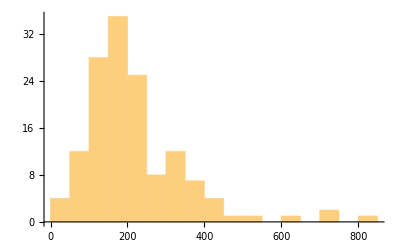

```mathematica
(*Filter and inspect the sizes of the keyword sets*)
flts=QuantileFilter[#,0.5]&/@tfidfs;
Length/@flts//Histogram
```

1.20179

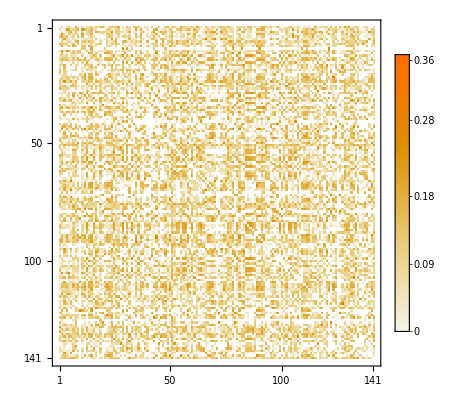

```mathematica
(*DistanceMatric does not parallelize, which is weird. Using Outer instead. Unfortunately, Outer is not smart enough to not to duplicate work with a commuting function, so there's double work being done, still.*)
AbsoluteTiming[closenessMatrix=Parallelize[Outer[df3,flts,flts]]][[1]]/60.
Save["latestClosenessMatrix",closenessMatrix];
MatrixPlot[closenessMatrix/.∞->0,PlotLegends->Automatic]
```

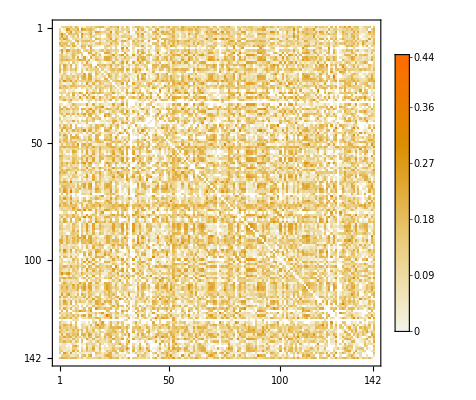

```mathematica
Get["latestClosenessMatrix"];MatrixPlot[closenessMatrix]
MatrixPlot[closenessMatrix/.∞->0,PlotLegends->Automatic]
```

#### 2.4.3 Thresholding connections

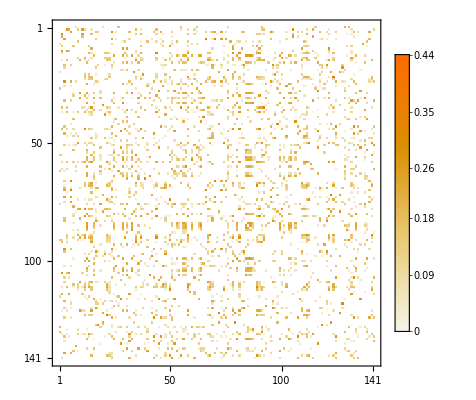

1

2890

```mathematica
dmmod=thres[closenessMatrix,0.02];MatrixPlot[dmmod/.∞->0,PlotLegends->Automatic]
Count[#,Except[0]]&/@(dmmod/.∞->0)//Min
Count[dmmod/.∞->0,Except[0],{2}]
```

## Graphing

### Defining labels, visuals, etc; uses also curated data

```mathematica
ShapeF[n_,coords_,scale_]:=If[vertexStatus[[n]]=="master",Disk[coords,0.02scale],Rectangle[coords-{0.02scale, 0.02scale},coords+{0.02scale,0.02scale}]]
VertexLabelFunction[x__]:=Module[
{lab,strs={x}},
lab=ToString/@strs[[1]];
MapIndexed[#1<>StringJoin[Table["\n"<>(strs[[i]][[#2]]//First//ToString),{i,Range[2,Length[strs]]}]]&,lab]
]
colors={hum=RGBColor@@Rescale[{87,112,194},{0,255.}],
	matlu=RGBColor@@Rescale[{228,169,36},{0,255.}],
	farm=RGBColor@@Rescale[{106,185,155},{0,255.}],
	bio=RGBColor@@Rescale[{126,190,39},{0,255.}],
	kayt=RGBColor@@Rescale[{238,213,39},{0,255.}]
}
```

{RGBColor[0.3411764705882353, 0.4392156862745098, 0.7607843137254902],RGBColor[0.8941176470588235, 0.6627450980392157, 0.1411764705882353],RGBColor[0.4156862745098039, 0.7254901960784313, 0.6078431372549019],RGBColor[0.49411764705882355, 0.7450980392156863, 0.15294117647058825],RGBColor[0.9333333333333333, 0.8352941176470589, 0.15294117647058825]}

```mathematica
(*Not pretty, but could be done*)
statuscolor=If[#=="master",White,Black]&/@authorstatus;
```

### Setting up the basic graph

Edge weights represent different values in different functions. WeightedAdjacencyMatrix and GraphLayouts use edge weights (i.e. entries in the distance matrix) as distances (e.g. natural lengths of springs). FindCommunity etc. use weights as a measure of connectivity. Care needs to be taken. Hence, edgeCloseness and edgeDistance are both used.

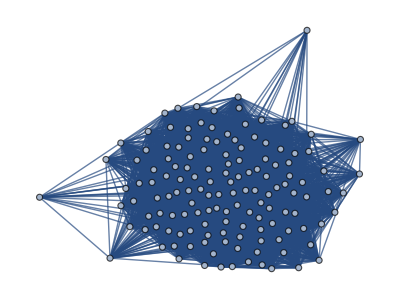

```mathematica
closenessGraph=WeightedAdjacencyGraph[closenessMatrix,
GraphStyle->"LargeNetwork",
GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding", "EdgeWeighted"->True}}
];
el=EdgeList[closenessGraph];
vl=VertexList[closenessGraph];
vlabels=VertexLabelFunction[vertexTitles,vertexAuthors,MapThread[StringJoin[#1,": ",#2]&,{vertexFaculties,vertexUnits}],vl,vertexAbstracts];
(*Closeness: [0,1], so that 0 ~ distant, 1 ~ co-located*)
edgeCloseness=Table[PropertyValue[{closenessGraph,el[[i]]},EdgeWeight],{i,1,EdgeCount[closenessGraph]}];
edgeCloseness=edgeCloseness//ewRescale;
(*edgeDistances: [0.01,1], so that 0.01 ~ minimun distance, 1 max distance*)
edgeDistances=1-edgeCloseness;
esCloseness=Table[el[[i]]->Directive[RGBColor@@Rescale[{182,217,176},{0,255.}],CapForm["Round"],Opacity[Clip[edgeCloseness[[i]],{0.6,1}]0.1],Thickness[Rescale[edgeCloseness[[i]],MinMax[edgeCloseness],{0.001,0.02}]]],{i,1,EdgeCount[closenessGraph]}];
distanceGraph=Graph[vl,el,EdgeWeight->edgeDistances]
```

Add properties to vertices and edges for export. Gephi can read .graphml pretty well, but note that Mathematica exports reals in a weird arbitrary-precision format. Use ToString to cast the numbers to a normal format (might still have problems with exp).

```mathematica
dg=SetProperty[{distanceGraph,vl},Table["Author"->vertexAuthors[[i]],{i,vl}]];
dg=SetProperty[{dg,vl},Table["Faculty"->vertexFaculties[[i]],{i,vl}]];
dg=SetProperty[{dg,el},Table["wgt"->ToString[edgeDistances[[i]]^20],{i,1,Length[el]}]];
Export["verkko.graphml",dg]
```

verkko.graphml

#### Distance-based graphing

```mathematica
(*Define a holder for the plain graph plot function with embedded metadata*)
wplot[vl_,el_,ews_]:=Graph[
	vl,el,
	GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True,"RepulsiveForcePower"->-2}},
	VertexLabels->Table[i->Placed[vlabels[[i]],Tooltip],{i,1,Length[vl]}],
	VertexShapeFunction->({Button[ShapeF[#2,#1,1],NotebookLocate[{vertexLinks[[#2]]//URL,None}] ]}&),
	VertexStyle->Table[vl[[i]]-> vertexColors[[vl[[i]]]],{i,1,VertexCount[closenessGraph]}],
	EdgeStyle->esCloseness,
	GraphStyle->"LargeNetwork",
	EdgeWeight->Clip[ews,{0.02,Max[ews]}]
]
```

Plot the theses with close connection indicated by a small distance between vertices. Transform the edge distances by raising to some large power for more pronounced separations.

```mathematica
g=wplot[vl,el,edgeDistances^20//ewRescale]
```

-Graphics-

Examine the distance graph with distances scaled with different powers (lengthy operation).

```mathematica
gds=Table[wplot[vl,el,Rescale[edgeDistances^pow]]//Show[#,PlotLabel->"Scaling power = "<>ToString[pow]]&,{pow,PowerRange[10,30,1.2]}];
hw=Table[Histogram[Rescale[edgeDistances^pow],PlotRange->{{0,1},{0,1500}},AxesLabel->{"Distance","counts"},ChartStyle->RGBColor[0.14*(pow)^0.5,0.5,0.5]],{pow,PowerRange[10,30,1.2]}];
GraphicsGrid[{gds,hw},ImageSize->Full]
```

Example: Find “shortest paths” from a thesis to another and highlight it on the graph.

```mathematica
path=FindShortestPath[g,3,88];
HighlightGraph[g,PathGraph[path],GraphHighlightStyle->"Dashed"]
```

-Graphics-

Find more about a vertex:

```mathematica
lookat=123;{vertexAuthors[[lookat]],vertexFaculties[[lookat]]}
vertexTitles[[lookat]]
tfidfs[[lookat]]//Take[#,10]&
```

#### Community-based graphing

```mathematica
(*Define a holder for a community plot with embedded metadata*)
commplot[vl_,el_,ews_]:=Module[
	{g},
	g=Graph[vl,el,EdgeWeight->ews];
	CommunityGraphPlot[g,FindGraphCommunities[g],
	EdgeLabels->None,
	VertexLabels->Table[vl[[i]]->Placed[vlabels[[VertexList[g][[i]]]],Tooltip],{i,1,VertexCount[g]}],
	VertexShapeFunction->({Button[ShapeF[#2,#1,1],NotebookLocate[{vertexLinks[[#2]]//URL,None}] ]}&),
	VertexStyle->Table[vl[[i]]-> vertexColors[[vl[[i]]]],{i,1,VertexCount[g]}],
	Method->"Hierarchical",GraphStyle->"LargeNetwork",EdgeStyle->esCloseness]
]
```

A basic community plot

```mathematica
commplot[vl,el,edgeCloseness^1.7]
```

Again, examine different scalings of closeness values:

```mathematica
gs=Table[commplot[vl,el,ewRescale[edgeCloseness^pow]],{pow,PowerRange[0.4,4,1.5]}];
hw=Table[Histogram[ewRescale[edgeCloseness^pow],{"Log",Automatic},PlotRange->{{0,1},{0,1500}},AxesLabel->{"closeness","counts"},ChartStyle->RGBColor[0.14*(pow+1)^2,0.5,0.5]],{pow,PowerRange[0.4,4,1.5]}];
GraphicsGrid[{gs,hw},ImageSize->Full]
```